```mathematica
n=4;
```

```mathematica
FinalN=1000;
```

```mathematica
SpecialVert={7,14,25,47,60,150};
```

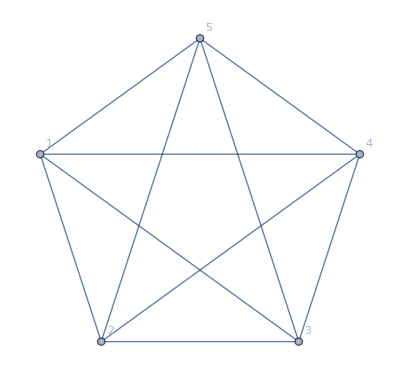

```mathematica
CoreGraph=Graph[CompleteGraph[n+1],VertexLabels->Automatic]
```

```mathematica
SeedRandom[63456];
Eta=RandomReal[{0,1},FinalN];
Eta[[SpecialVert]]={0.5,0.9,0.7,0.9,0.6,0.9}
```

{0.5,0.9,0.7,0.9,0.6,0.9}

```mathematica
NodeAdd[g_,n_]:=(Module[{Newg,x},
x=VertexCount[g]+1;
Newg=VertexAdd[g,x];
Newg=EdgeAdd[Newg,UndirectedEdge[x,#]&/@RandomChoice[Eta[[1;;x-1]]*VertexDegree[g]-> VertexList[g],n]];
Newg
]
)
(*NodeAdd[g_]:=(Module[{Newg,x},
x=VertexCount[g]+1;
Newg=VertexAdd[g,x];
Do[Newg=EdgeAdd[Newg,x<->RandomChoice[Eta[[1;;x-1]]*VertexDegree[g]-> VertexList[g]]],n];
Newg
]
)*)
```

```mathematica
SeedRandom[65354];
{t,FinalGraph}=Timing[Nest[(NodeAdd[#,n]&),CoreGraph,FinalN-5]];t
```

2.1875

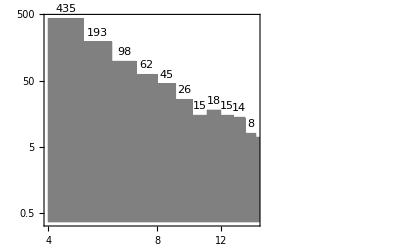

```mathematica
Histogram[VertexDegree[FinalGraph],ScalingFunctions->{"Log","Log"},ChartStyle->Gray,LabelingFunction->Above,PlotTheme->"Web"]
```

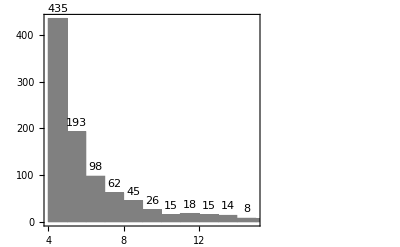

```mathematica
Histogram[VertexDegree[FinalGraph],ChartStyle->Gray,LabelingFunction->Above,PlotTheme->"Web"]
```

```mathematica
GraphEvolution=NestList[(NodeAdd[#,n]&),CoreGraph,FinalN-5];
```

```mathematica
DegreeEvolution[v_,step_,n_]:=(Module[{Steps},
Steps=Range[v-(n+1)+1,FinalN-(n+1)+1,step];
Transpose[{Steps,(VertexDegree[#,v]&)/@GraphEvolution[[v-(n+1)+1;;FinalN-(n+1)+1;;step]]}]
]
)
```

```mathematica
Ds=DegreeEvolution[#,10,n]&/@SpecialVert;
```

```mathematica
ListLogLogPlot[Ds,PlotLabels->SpecialVert,Joined->True]
```

-Graphics-

```mathematica
ListPlot[Ds,PlotLabels->SpecialVert,Joined->True]
```

-Graphics-

```mathematica
LinearModelFit[Log[DegreeEvolution[7,10,n]],x,x]
LinearModelFit[Log[DegreeEvolution[14,10,n]],x,x]
LinearModelFit[Log[DegreeEvolution[25,10,n]],x,x]
LinearModelFit[Log[DegreeEvolution[150,10,n]],x,x]
```

FittedModel[0.566613+0.461006 x]

FittedModel[-0.105039+0.706943 x]

FittedModel[-0.897852+0.801619 x]

FittedModel[-2.23019+0.698794 x]

```mathematica
FittedModel[11.668205220522053+0.035284728472847283 x]
L
```